## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.0799688 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 25, 2020, time: 21:49:52

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/best-worst-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.0799688 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## raw data

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=meanRCS[[1]];
{M,𝒩}=Dimensions[meanRCS]
```

{28,361}

```mathematica
S=meanRCSᵀ;
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## plot routines

### ticks

```mathematica
iwant={3,10,20,30};
ihave=(2/27 #-11/9)&/@iwant;
```

```mathematica
ticksA={{Automatic,Automatic},{{ihave,iwant}ᵀ,Automatic}};
```

### data v fit

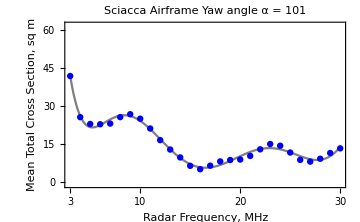

```mathematica
Clear[plotDataFit];
plotDataFit[dataVector_List,mesh_List,solutionFunction_Symbol,index_Integer]:=Module[{meshmax,meshmin},
(* boundary points *)
{meshmin,meshmax}={Max[#],Min[#]}&@mesh;
(* data *)
glistplot=ListPlot[{mesh,dataVector}ᵀ,
PlotStyle->Blue];
(* solution *)
gplot=Plot[solutionFunction[x],{x,meshmin,meshmax},Frame->True,
FrameTicks->ticksA,
PlotStyle->{Black,Opacity[0.5]}];
gout=Show[{gplot,glistplot},
ipad,
isize,
Axes->{False,False},
PlotStyle->Purple,
PlotRange->{Automatic,{-1,62}},
PlotLabel->"Sciacca Airframe"<>lf<>"Yaw angle α = "<>ToString[index-181],
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"}];
Return[gout]];
plotDataFit[b,μ,g,kbest]
```

### residual fit error

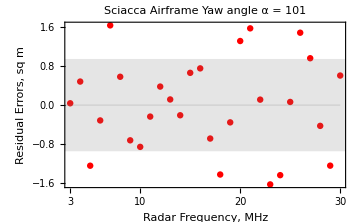

```mathematica
Clear[plotResidualError];
plotResidualError[residualErrorVector_List,mesh_List,index_Integer]:=Module[{meshmax,meshmin,mean,sd, hi,lo},
(* boundary points *)
{meshmin,meshmax}={Max[#],Min[#]}&@mesh;
(* characterize residuals *)
mean=Mean[residualErrorVector];
sd=StandardDeviation[residualErrorVector];
hi=mean+sd;
lo=mean-sd;
(* data *)
glistplot=ListPlot[{mesh,residualErrorVector}ᵀ,
ipad,
isize,
PlotStyle->Red,
PlotRange->Full,
PlotLabel->"Sciacca Airframe"<>lf<>"Yaw angle α = "<>ToString[-180+index-1],
Frame->True,
FrameTicks->ticksA,
FrameLabel->{"Radar Frequency, MHz","Residual Errors, sq m"},
PlotStyle->Red];
(* adornments *)
gmean=Graphics[{Thick,Gray,Opacity[0.2],Line[{{-1.1,mean},{1,mean}}]}];
gbox=Graphics[{Gray,Opacity[0.2],Rectangle[{-1.1,lo},{1.1,hi}]}];
Return[Show[{glistplot,gbox,gmean},Axes->False]]];
plotResidualError[r,μ,kbest]
```

### bar chart

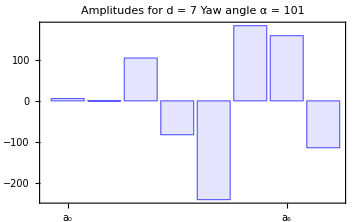

```mathematica
Clear[plotBarChart];
plotBarChart[solutionVector_List,index_Integer,d_Integer]:=Module[{},
BarChart[solutionVector,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>"Yaw angle α = "<>ToString[index-181],
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,25}],Automatic}},
ipad,
isize]];
(* test *)
plotBarChart[c,kbest,d]
```

### error bars

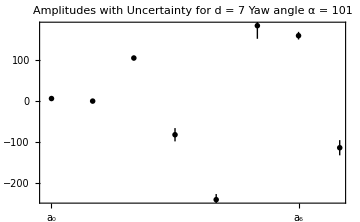

```mathematica
Clear[errorBars];
errorBars[solutionVector_List,uncertaintyVector_List,index_Integer,d_Integer]:=Module[{},
ebars=Table[
Around[solutionVector[[k]],uncertaintyVector[[k]]]
,{k,Length[uncertaintyVector]}];
gebars=ListPlot[ebars,
ipad,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,25}],Automatic}},
PlotLabel->"Amplitudes with Uncertainty for d = "<>ToString[d]<>lf<>"Yaw angle α = "<>ToString[index-181],
PlotStyle->Black,
PlotRange->Full];
Return[gebars]];
(* gg=Graphics[{Gray,Opacity[0.15],Rectangle[{12.5,-0.2},{25.5,0.25}]}]; *)
errorBars[c,𝓈,k,d]
```

## best case

```mathematica
kbest=282;
type="best";
b=meanRCSᵀ[[kbest]]
```

{41.9374,25.6377,22.9358,22.8313,23.1055,25.6561,26.8032,25.0273,21.1427,16.549,12.8073,9.6908,6.36494,5.02343,6.41749,8.11375,8.66363,8.86092,10.2919,12.9025,15.0031,14.3221,11.6355,8.72225,8.02749,9.17217,11.435,13.2785}

## worst case

```mathematica
kworst=181;
type="worst";
b=meanRCSᵀ[[kworst]]
```

{39.4129,38.1899,42.8299,42.3212,32.6751,27.6474,23.6392,22.8893,23.0467,17.3097,7.63058,7.16701,10.8886,7.57704,13.0031,21.2171,21.0519,19.1782,25.8174,25.435,17.7161,15.8002,14.3355,11.5346,19.0441,27.8603,27.617,28.7245}

```mathematica
c
```

{14.0789,39.6621,25.6559,-269.393,2.28237,419.331,-7.00872,-194.872}

## run data

```mathematica
k=kworst;
```

### prep

```mathematica
ν=Range[3,30];
```

```mathematica
μ=(2/27 #-11/9)&/@ν;
```

### pose problem

```mathematica
d=7;
basis=Table[𝓍^k,{k,0,d}];
𝒩=d+1;
m=Length[μ]
```

28

```mathematica
one=Table[1,{m}];
A={one};
vector=1;
Do[
vector=vector μ;
AppendTo[A,vector]
,{k,d}];
A=Aᵀ;
W=A†.A;
Winv=Inverse[W];
det=Det[W];
```

```mathematica
s=SingularValueList[A];
κ=First[s]/Last[s];
```

### solve

```mathematica
c=LeastSquares[A,b];
r=A.c-b;
te=r.r;
g[𝓍_]=c.basis;
𝓈=√((r.r)/(m-𝒩)Diagonal[Winv]);
sn=Abs[c]/𝓈;
```

### plots

```mathematica
g001=plotDataFit[b,μ,g,k];
g002=plotResidualError[r,μ,k];
g003=plotBarChart[c,k,d];
g004=errorBars[c,𝓈,k,d];
```

### export

```mathematica
Export[dirGraph<>"monomial-"<>type<>"-datavfit"<>".pdf",g001]
Export[dirGraph<>"monomial-"<>type<>"-residual"<>".pdf",g002]
Export[dirGraph<>"monomial-"<>type<>"-barchart"<>".pdf",g003]
Export[dirGraph<>"monomial-"<>type<>"-errorbar"<>".pdf",g004]
```

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/graphics/monomial-worst-datavfit.pdf

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/graphics/monomial-worst-residual.pdf

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/graphics/monomial-worst-barchart.pdf

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/graphics/monomial-worst-errorbar.pdf

## disk

### angles

```mathematica
ω=100;
γ=Table[
2π k/ω
,{k,ω}];
```

```mathematica
o3={0,0,0};
λ=1.1;
```

```mathematica
pts={Cos[#],Sin[#],0}&/@γ;
gpoly=Graphics3D[{Blue,Opacity[0.5],Polygon[pts]}];
arrw=Graphics3D[{Red,Thick,Arrow[{o3,{1.05,0,0}}]}];
arrb=Graphics3D[{Green,Thick,Arrow[{o3,1.05{Cos[101Degree],Sin[101Degree],0}}]}];
gtexta=Text["90°",{0,λ,0},{-2,0}];
gtextb=Text["-90°",{0,-λ,0},{2,0}];
gtextc=Text["α=0",{λ,0,0},{0,1}];
gtextd=Text["±180°",{-λ,0,0},{0,-1}];
tickLeft=Line[{{0,-1.05,0},{0,-0.95,0}}];
tickRight=Line[{{0,0.95,0},{0,1.05,0}}];
tickBack=Line[{{-0.95,0,0},{-1.05,0,0}}];
gticks=Graphics3D[{Thick,tickLeft,tickRight,tickBack}];
gmarks=Graphics3D[{gtexta,gtextb,gtextc,gtextd}];
gbest=Show[{gpoly,arrb,arrw,gmarks,gticks},
ViewPoint->{Above,Right},
Boxed->False]
```

-Graphics3D-

```mathematica
Export[dirGraph<>"best-worst-yaw.pdf",gbest]
```

/Users/dantopa/Mathematica_files/io/ert/mercury/snake/graphics/best-worst-yaw.pdf

## table of values

```mathematica
c
```

{14.0789,39.6621,25.6559,-269.393,2.28237,419.331,-7.00872,-194.872}

```mathematica
k=kworst
```

181

```mathematica
Table[
index=k+1;
str="            $c_{"<>ToString[k]<>"}$ ";
str=str<>"& = & ";
(* amplitude *)
a=c[[index]];
ipart=IntegerPart[a];
fpart=FractionalPart[Abs[a]];
(* amp to string *)
str=str<>"$"<>ToString[ipart]<>"$";
num=ToString[Round[(1000 fpart)/10]];
str=str<>" & ";
str=str<>"$"<>num<>"$";
str=str<>" & $@pm$ & ";
(* error *)
a=𝓈[[index]];
ipart=IntegerPart[a];
fpart=FractionalPart[Abs[a]];
(* err to string *)
str=str<>"$"<>ToString[ipart]<>"$";
num=ToString[Round[(1000 fpart)/10]];
str=str<>" & ";
str=str<>"$"<>num<>"$ @@";
Print[str];
,{k,0,d}];
```

$c_{0}$ & = & $14$ & $8$ & $@pm$ & $1$ & $61$ @@

$c_{1}$ & = & $39$ & $66$ & $@pm$ & $8$ & $23$ @@

$c_{2}$ & = & $25$ & $66$ & $@pm$ & $18$ & $52$ @@

$c_{3}$ & = & $-269$ & $39$ & $@pm$ & $56$ & $56$ @@

$c_{4}$ & = & $2$ & $28$ & $@pm$ & $47$ & $90$ @@

$c_{5}$ & = & $419$ & $33$ & $@pm$ & $111$ & $62$ @@

$c_{6}$ & = & $-7$ & $1$ & $@pm$ & $32$ & $58$ @@

$c_{7}$ & = & $-194$ & $87$ & $@pm$ & $64$ & $72$ @@

```mathematica
c
```

{31.6443,-34.3301,16.4882,-3.15289,0.294823,-0.0143006,0.000345972,-3.3052×10^-6}

```mathematica
𝓈
```

{10.1201,11.0579,4.03277,0.68148,0.0604026,0.00289606,0.0000710405,6.98343×10^-7}

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```